```mathematica
2-2
```

0

# The harmonically dithered pendulum

Nicholas Wheeler
Reed College Physics Department
September 2008

The following DE was first studied by Emile Mathieu, in 1868.

```mathematica
Hyperlink["Emile Mathieu","http://www.gap-system.org/~history/Biographies/Mathieu_Emile.html"]
```

```mathematica
Hyperlink["Mathieu functions","http://en.wikipedia.org/wiki/Mathieu_function"]
```

```mathematica
DSolve[x''[t]+(a-2q Cos[2t])x[t]==0,x[t],t]
```

{{x[t]→C[1] MathieuC[a,q,t]+C[2] MathieuS[a,q,t]}}

```mathematica
MathieuC[a,q,t]== MathieuC[a,q,-t]
MathieuS[a,q,t]==-MathieuS[a,q,-t]
```

True

True

```mathematica
MathieuC[a,0,t]
 MathieuS[a,0,t]
```

Cos[√a t]

Sin[√a t]

Periodic Solutions

For given q ≠ 0 the Mattieu functions are periodic only for certain a-values. It is known that there exist points in {a, q}-space where the Mattieu functions have period kπ (k = 1, 2, 3, 4, …). Especial importance attaches in the theory to cases k = 1 and k = 2.

It appears to be standard practice to write

Mattieu[a[q],q,t]

and to attempt to discover the structure forced upon a[q]  by the requirement that  Mattieu[a[q], q, t] be periodic in t. The function turns out to be multi-valued, so people write

MattieuC[MathieuCharacteristicA[r,q], q, t]
 MattieuS[MathieuCharacteristicB[r,q], q, t]

where r can be either an integer or a rational number.

Here I show how MathieuC evolves away from Cos:

```mathematica
Manipulate[Plot[{Cos[t],MathieuC[MathieuCharacteristicA[1,q], q, t]},{t,-2π,2π}, Ticks->{{-2π,-π,π,2π},{-1,1}}],{q,0,60}]
```

```mathematica
Manipulate[Plot[ MathieuC[MathieuCharacteristicA[r,q], q, t],{t,-2π,2π}, PlotRange->{-2,2}],{r,0,5,1},{q,0,60}]
```

Here MathieuS evolves away from Sin:

```mathematica
Manipulate[Plot[{Sin[t],MathieuS[MathieuCharacteristicB[1,q], q, t]},{t,-2π,2π}, Ticks->{{-2π,-π,π,2π},{-1,1}}],{q,0,60}]
```

```mathematica
Manipulate[Plot[ MathieuS[MathieuCharacteristicB[r,q], q, t],{t,-2π,2π}, PlotRange->{-2,2}],{r,1,5,1},{q,0,20}]
```

### Associated phase plots:

```mathematica
D[ MathieuC[MathieuCharacteristicA[r,q], q, t],t]
D[ MathieuS[MathieuCharacteristicB[r,q], q, t],t]
```

MathieuCPrime[MathieuCharacteristicA[r,q],q,t]

MathieuSPrime[MathieuCharacteristicB[r,q],q,t]

```mathematica
Manipulate[ParametricPlot[{ MathieuC[MathieuCharacteristicA[r,q], q, t],MathieuCPrime[MathieuCharacteristicA[r,q], q, t]},{t,0,4π}, PlotRange->{{-2,2},{-8,8}}],{r,0,5,1},{q,0,20}]
```

```mathematica
Manipulate[ParametricPlot[{ MathieuS[MathieuCharacteristicB[r,q], q, t],MathieuSPrime[MathieuCharacteristicB[r,q], q, t]},{t,0,4π}, PlotRange->{{-2,2},{-8,8}}],{r,1,5,1},{q,0,20}]
```

### Characteristics

Much of the labor in the theory of Mathieu functions goes into the complex business of figuring out the curves a(q) that points on the {a,q} plane where the Mathieu functions are periodic.

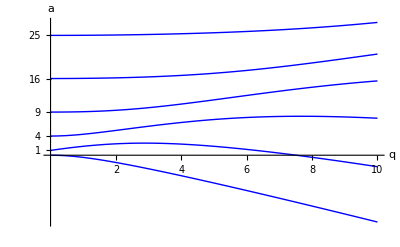

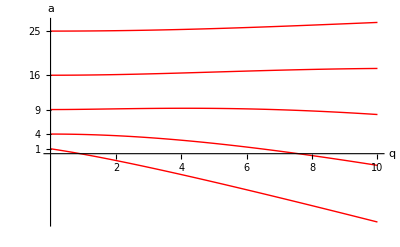

```mathematica
ACharacteristics=Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicA[1,q],MathieuCharacteristicA[2,q],MathieuCharacteristicA[3,q],MathieuCharacteristicA[4,q],MathieuCharacteristicA[5,q]}, {q,0,10}, PlotStyle->{Blue}, AxesLabel->{q,a},Ticks->{{2,4,6,8,10},{1,4,9,16,25}}]

BCharacteristics=Plot[{MathieuCharacteristicB[1,q],MathieuCharacteristicB[2,q],MathieuCharacteristicB[3,q],MathieuCharacteristicB[4,q],MathieuCharacteristicB[5,q]}, {q,0,10},PlotStyle->{Red}, AxesLabel->{q,a}, Ticks->{{2,4,6,8,10},{1,4,9,16,25}}]
```

These curves resolve the {a,q} plane into regions of STABILITY (bounded variation) and INSTABILITY (unbounded variation).

```mathematica
Sector0=Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicB[1,q]}, {q,0,60},Filling->{1->{2}}];
Sector00=Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicB[1,q]}, {q,0,15},Filling->{1->{2}}];
Sector1=Plot[{MathieuCharacteristicA[1,q],MathieuCharacteristicB[2,q]}, {q,0,60},Filling->{1->{2}}];
Sector10=Plot[{MathieuCharacteristicA[1,q],MathieuCharacteristicB[2,q]}, {q,0,15},Filling->{1->{2}}];
Sector2=Plot[{MathieuCharacteristicA[2,q],MathieuCharacteristicB[3,q]}, {q,0,60},Filling->{1->{2}}];
Sector20=Plot[{MathieuCharacteristicA[2,q],MathieuCharacteristicB[3,q]}, {q,0,15},Filling->{1->{2}}];
Sector3=Plot[{MathieuCharacteristicA[3,q],MathieuCharacteristicB[4,q]}, {q,0,60},Filling->{1->{2}}];
Sector30=Plot[{MathieuCharacteristicA[3,q],MathieuCharacteristicB[4,q]}, {q,0,15},Filling->{1->{2}}];
Sector4=Plot[{MathieuCharacteristicA[4,q],MathieuCharacteristicB[5,q]}, {q,0,60},Filling->{1->{2}}];
Sector40=Plot[{MathieuCharacteristicA[4,q],MathieuCharacteristicB[5,q]}, {q,0,15},Filling->{1->{2}}];
Sector5=Plot[{MathieuCharacteristicA[5,q],MathieuCharacteristicB[6,q]}, {q,0,60},Filling->{1->{2}}];
Sector50=Plot[{MathieuCharacteristicA[5,q],MathieuCharacteristicB[6,q]}, {q,0,15},Filling->{1->{2}}];
```

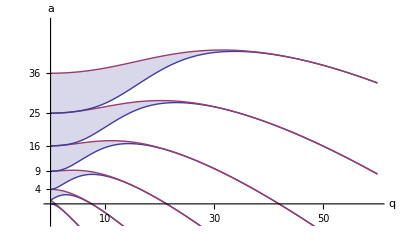

```mathematica
Show[{Sector0,Sector1,Sector2,Sector3,Sector4,Sector5}, PlotRange->{-5,50},Ticks->{{10,20,30,40,50,60},{4,9,16,25,36}}, AxesLabel->{q,a}]
```

Here is a magnified view of the left edge of the preceding figure:

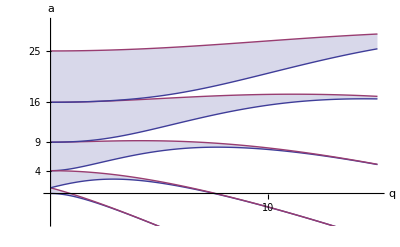

```mathematica
Show[{Sector00,Sector10,Sector20,Sector30,Sector40}, PlotRange->{-5,30},Ticks->{{10,20,30,40,50,60},{4,9,16,25,36}}, AxesLabel->{q,a}]
```

From the following figure we see that blue A-characteristics define the bottoms of the SHADED STABLE REGIONS, the red B-characteristics define their top:

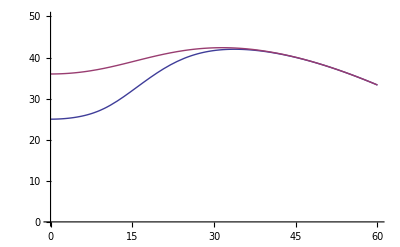

```mathematica
Plot[{MathieuCharacteristicA[5,q],MathieuCharacteristicB[6,q]}, {q,0,60}, PlotRange->{0,50}]
```

Stable Aperiodic Solutions

The motion is aperiodic but stable (does not run away) if {a,q} lies in the shaded region.  To illustrate the point, I set q = 3 and let a range up the vertical line in the following figure:

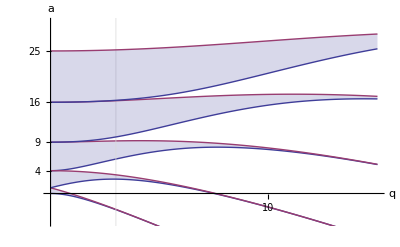

```mathematica
Show[{Sector00,Sector10,Sector20,Sector30,Sector40}, PlotRange->{-5,30},Ticks->{{10,20,30,40,50,60},{4,9,16,25,36}}, AxesLabel->{q,a}, GridLines->{{3},{}}]
```

We start at -4, in a region of instability, pass through a brief region of stability, then through successive regions of instability that get progressively briefer, alternating regions of stability that get progressively longer. NOTE: Mathematica attributes tiny imaginary parts to the Mathieu functions in unstable regions; to get Mathematica to plot I have had to snip those off.

```mathematica
Manipulate[ ParametricPlot[{Re[MathieuC[a,3,t]],Re[MathieuCPrime[a,3,t]]},{t,0,20π},PlotRange->{{-10,10},{-10,10}}],{a,-4,12}]
```

In the following figure we move along near the stable edge of an unstable region, and witness the slow explosion of the orbit:

```mathematica
Manipulate[ ParametricPlot[{Re[MathieuC[MathieuCharacteristicA[3,q]-1/1000,q,t]],Re[MathieuCPrime[MathieuCharacteristicA[3,q]-1/1000,q,t]]},{t,0,100},PlotRange->{{-6,6},{-8,8}}],{q,0,20}]
```

### Inverted pendulum

Small amplitude motion is described by a Mathieu equation with a negative a-parameter. Here is the sector of primary interest

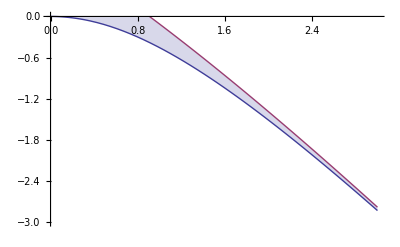

```mathematica
Sector000=Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicB[1,q]}, {q,0,3},Filling->{1->{2}}, PlotRange->{-3,0}]
```

Here is the leading member of an infinite family of sectors of diminishing interest:

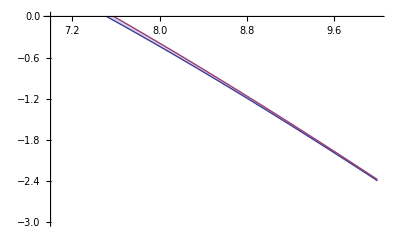

```mathematica
Sector100=Plot[{MathieuCharacteristicA[1,q],MathieuCharacteristicB[2,q]}, {q,7,10},Filling->{1->{2}}, PlotRange->{-3,0}]
```

I prepare to construct a close-up view of the stable sector of primary interest—the "magic sector."

```mathematica
FindRoot[MathieuCharacteristicB[1,q],{q,.9}]
```

{q→0.908046}

```mathematica
Q=0.9080463337345777
```

0.908046

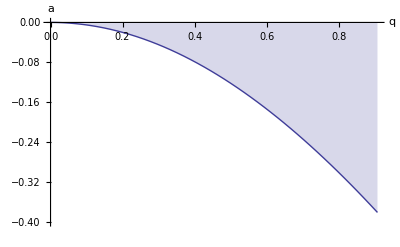

```mathematica
Sector000=Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicB[1,q]}, {q,0,Q},Filling->{1->{2}}, PlotRange->{-0.4,0},AxesLabel->{q,a}]
```

The lower bound is well approximated by (see Abramowitz & Stegun, 20.2.25 on page 724)

```mathematica
LowerCurve[q_]:=-1/2 q^2+7/128 q^4-29/2304 q^6+68687/18874368 q^8
```

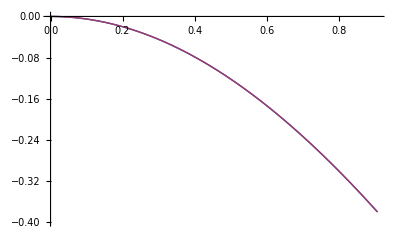

```mathematica
Plot[{MathieuCharacteristicA[0,q],LowerCurve[q]},{q,0,Q}, PlotRange->{-0.4,0}]
```

We can expect stable motion if

```mathematica
0<q<Q
```

and

```mathematica
LowerCurve[q]≈-1/2 q^2<a<0
```

which in physical variables becomes

```mathematica
-1/2(2 A/R)^2<-(2 ω/Ω)^2
```

or

```mathematica
A/R>√2 ω/Ω
```

### First Example

Set

q=8/10<Q

```mathematica
a=LowerCurve[8/10]/2//N
```

-0.150145

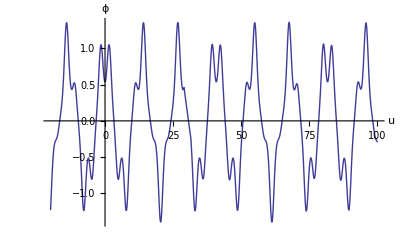

```mathematica
Plot[MathieuC[-.15,0.8,u],{u,-20,100}, AxesLabel->{u,ϕ}]
```

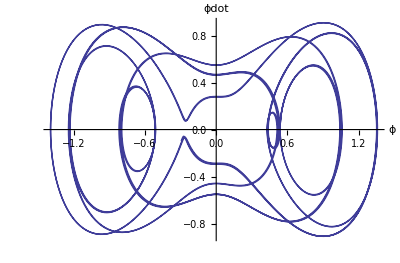

```mathematica
ParametricPlot[{MathieuC[-.15,0.8,u],MathieuCPrime[-.15,0.8,u]},{u,0,100},AxesLabel->{ϕ,"ϕdot"}]
```

The odd Mathieu function leads—with identical parameters—to quite a different phase plot:

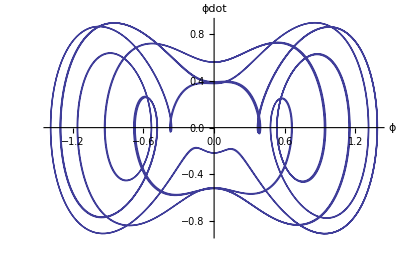

```mathematica
ParametricPlot[{MathieuS[-.15,0.8,u],MathieuSPrime[-.15,0.8,u]},{u,0,100},AxesLabel->{ϕ,"ϕdot"}]
```

Next I show what happens as the a-parameter sweeps down the line q = 0.8 shown in the following figure:

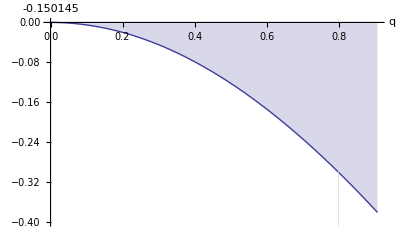

```mathematica
Sector000=Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicB[1,q]}, {q,0,Q},Filling->{1->{2}}, PlotRange->{-0.4,0},AxesLabel->{q,a}, GridLines->{{0.8},{}}]
```

```mathematica
Manipulate[ParametricPlot[{MathieuC[-a,0.8,u],MathieuCPrime[-a,0.8,u]},{u,0,20},AxesLabel->{ϕ,"ϕdot"}, PlotRange->{-2,2}],{a,0.05,.25}]
```

```mathematica
Manipulate[ParametricPlot[{MathieuC[-a,0.8,u],MathieuCPrime[-a,0.8,u]},{u,0,200},AxesLabel->{ϕ,"ϕdot"}, PlotRange->{-2,2}],{a,0.05,.25}]
```

An assortment of especially simple (complexly periodic) patterns are encountered as one sweeps through the continuum of figures. Here is an example:

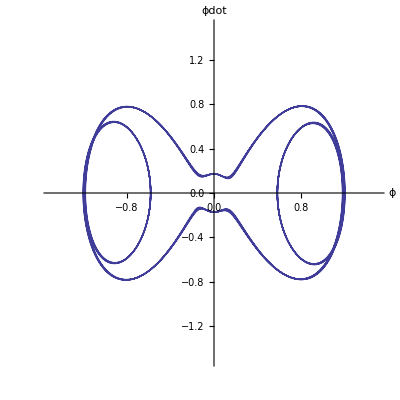

```mathematica
ParametricPlot[{MathieuC[-.2194,0.8,u],MathieuCPrime[-.2194,0.8,u]},{u,0,100},AxesLabel->{ϕ,"ϕdot"}, PlotRange->{-1.5,1.5}]
```

### Second Example

```mathematica
q=4/10
```

```mathematica
LowerCurve[4/10]/2//N
```

-0.0393246

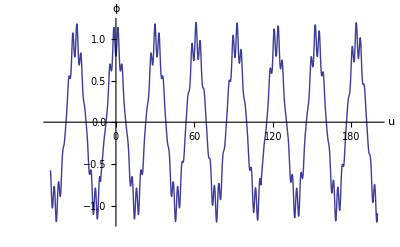

```mathematica
Plot[MathieuC[-.04,0.4,u],{u,-50,200}, AxesLabel->{u,ϕ}]
```

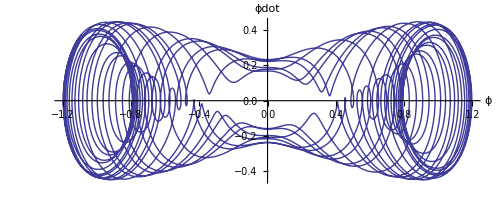

```mathematica
ParametricPlot[{MathieuC[-.04,0.4,u],MathieuCPrime[-.04,0.4,u]},{u,0,200},AxesLabel->{ϕ,"ϕdot"}]
```

### Third Example

```mathematica
q=2/100
```

```mathematica
LowerCurve[2/100]/2//N
```

-0.0000999956

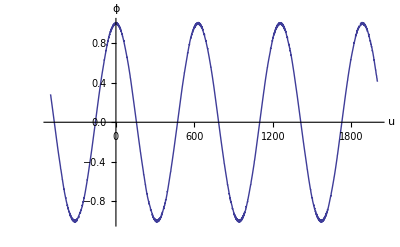

```mathematica
Plot[MathieuC[-.0001,0.02,u],{u,-500,2000}, AxesLabel->{u,ϕ}]
```

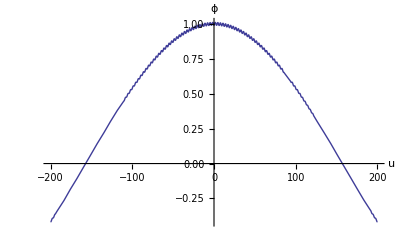

```mathematica
Plot[MathieuC[-.0001,0.02,u],{u,-200,200}, AxesLabel->{u,ϕ}]
```

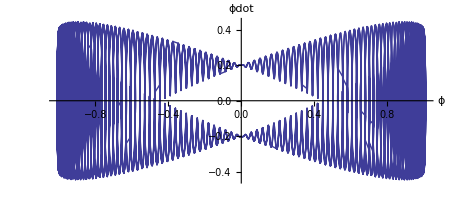

```mathematica
ParametricPlot[{MathieuC[-.0001,0.02,u],20MathieuCPrime[-.0001,0.02,u]},{u,0,2000},AxesLabel->{ϕ,"ϕdot"}, PlotPoints->150]
```

### Stability in the Second Sector

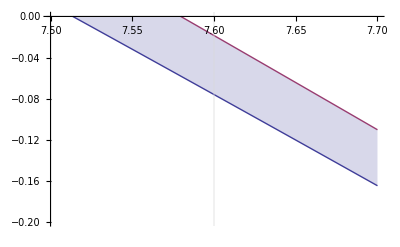

```mathematica
Sector100B=Plot[{MathieuCharacteristicA[1,q],MathieuCharacteristicB[2,q]}, {q,7.5,7.7},Filling->{1->{2}}, PlotRange->{-0.2,0}, GridLines->{{7.6},{}}]
```

```mathematica
q=7.6
a=-0.05
```

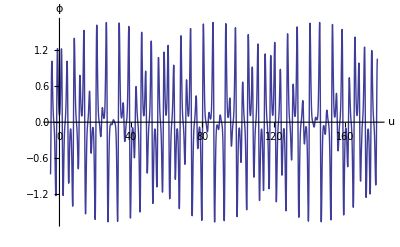

```mathematica
Plot[MathieuC[-0.05,7.6,u],{u,-5,178}, AxesLabel->{u,ϕ}]
```

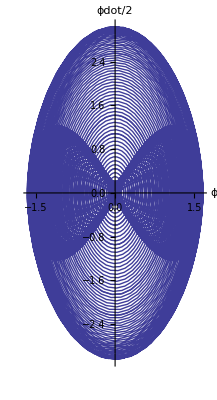

```mathematica
ParametricPlot[{MathieuC[-0.05,7.6,u],1/2 MathieuCPrime[-0.05,7.6,u]},{u,0,450},AxesLabel->{ϕ,"ϕdot/2"}, PlotPoints->150]
```

```mathematica
Manipulate[ParametricPlot[{MathieuC[-a,7.6,u],MathieuCPrime[-a,7.6,u]},{u,0,150},AxesLabel->{ϕ,"ϕdot"}, PlotRange->{-8,8}],{a,0.02,0.075}]
```

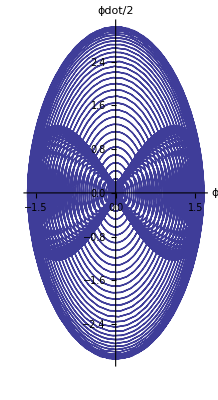

```mathematica
ParametricPlot[{MathieuS[-0.05,7.6,u],1/2 MathieuSPrime[-0.05,7.6,u]},{u,0,450},AxesLabel->{ϕ,"ϕdot/2"}, PlotPoints->150]
```

### Literature

For a short account, with useful references and a cute applet, visit

```mathematica
Hyperlink["Inverted Pendulum","http://en.wikipedia.org/wiki/Inverted_pendulum"]
```

Discussion of the inverted pendulum can be found in the theses of Leonard Clapp, "A pendulum with oscillating support" (1979) and Eric Lindsey, "Parametric resonance in systms of vertically driven pendulums" (2008).

Several  non-pendular systems lead to the same mathematics, and exhibit analogous behavior. One is the "Paul trap," in which connection see Christopher Knowlton, "Quadrupole traps"  (Reed College thesis, 2008). See also

M. H. Friedman, J. E. Campana, L. Kelner, E. H. Seeliger & A. L. Yergey, "The inverted pendulum: A mechanical analog of the quadrupole mass filter,"AJP 50, 924 (1982)

and these web sites:

```mathematica
Hyperlink["Paul trap","http://en.wikipedia.org/wiki/Quadrupole_ion_trap"]
```

```mathematica
Hyperlink["Quadrupole trap movie","http://www.iontrap.umd.edu/research/microspheres/Rotating%20Saddle.MOV"]
```